1/500000

25.9487

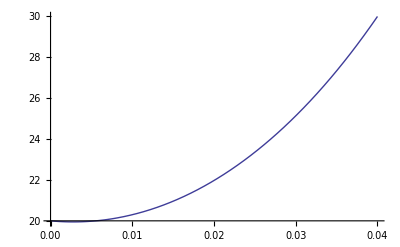

```mathematica
(* FIN - Numerical Solution - const k and A fin - p. 45 *)
To = 30. ;
(* °C *)
Tend=40. ;
(* °C *)
W= 0.01;
(*meter*)
THICK=1. ;
(*meters*)
h = 10. ;
(*W/m^2C *)
k = 3. ;
(*W/mC *)
ALPHA = 2*10^-6;
(*kg/m^3 x J/kg C*)
Tenv = 10. ;
(* °C *)
Acs = W*THICK;
(*cross sectional area m^2 *)
P = 2*(W+THICK);
(* Perimeter meters ^2 *)
HPKA = (h*P*k*Acs)^0.5;
TEMP = To-Tenv;
(*m=(h*P/(k*Acs))^0.5; *)

(* prescribed tip temperature case *)
m=(h*P/(k*Acs))^0.5
Subscript[x, 1]=0.0;
Subscript[x, 2]=0.04;
Subscript[T, 1]=30;
Subscript[T, 2]=40;
Subscript[T, e]=10;
Subscript[θ, 1]=Subscript[T, 1]-Subscript[T, e];
Subscript[θ, 2]=Subscript[T, 2]-Subscript[T, e];
solution2=NDSolve[{θ''[x] - m^2 *θ[x]== 0,θ[Subscript[x, 1]]==Subscript[θ, 1],θ[Subscript[x, 2]]==Subscript[θ, 2]},θ,{x,Subscript[x, 1],Subscript[x, 2]}];
PS1=Plot[Evaluate[θ[x]/.First[solution2]],{x,Subscript[x, 1],Subscript[x, 2]},PlotRange->All]
```

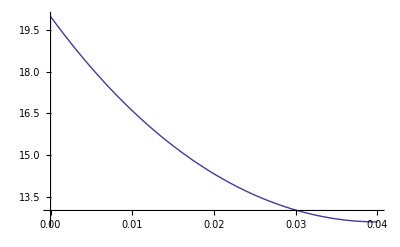

```mathematica
(* Adiabatic tip condition *)
m=(h*P/(k*Acs))^0.5;
Subscript[x, 1]=0.0;
Subscript[x, 2]=0.04;
Subscript[T, 1]=30;
Subscript[T, 2]=40;
Subscript[T, e]=10;
Subscript[θ, 1]=Subscript[T, 1]-Subscript[T, e];
(*Subscript[θ, 2]=Subscript[T, 2]-Subscript[T, e];  *)
solution2=NDSolve[{θ''[x] - m^2 *θ[x]== 0,θ[Subscript[x, 1]]==Subscript[θ, 1],θ'[Subscript[x, 2]]==0},θ,{x,Subscript[x, 1],Subscript[x, 2]}];
PS=Plot[Evaluate[θ[x]/.First[solution2]],{x,Subscript[x, 1],Subscript[x, 2]},PlotRange->All]
```

1.03795

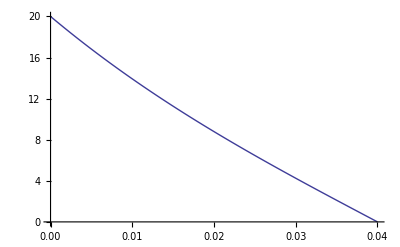

```mathematica
(* Infinite tip condition *)
m=(h*P/(k*Acs))^0.5;
Subscript[x, 1]=0.0;
Subscript[x, 2]=0.04;
Subscript[T, 1]=30;
Subscript[T, 2]=40;
Subscript[T, e]=10;
Subscript[θ, 1]=Subscript[T, 1]-Subscript[T, e];
(*Subscript[θ, 2]=Subscript[T, 2]-Subscript[T, e];  *)
INF = m*(Subscript[x, 2]-Subscript[x, 1])
solution2=NDSolve[{θ''[x] - m^2 *θ[x]== 0,θ[Subscript[x, 1]]==Subscript[θ, 1],θ[Subscript[x, 2]]==0},θ,{x,Subscript[x, 1],Subscript[x, 2]}];
PS1=Plot[Evaluate[θ[x]/.First[solution2]],{x,Subscript[x, 1],Subscript[x, 2]},PlotRange->All]
```

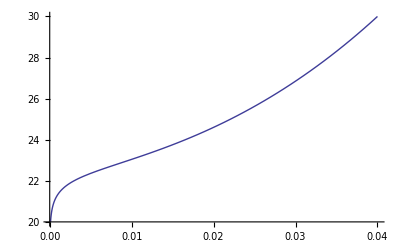

```mathematica
(* Can do convective tip for homework *)



(* POSSIBILITY FOR NON CONSTANT CROSS SECTIONAL AREA FIN *)

(* CYLINDRICAL FIN - PRESCRIBED TIP *)
h=10;
t=0.01;
k=3;
γ=Sqrt [2*h/(k*t)];
Subscript[T, 0]=30;
Subscript[T, 1]=40;
Subscript[T, a]=10;
Subscript[θ, 0]=Subscript[T, 0]-Subscript[T, a];
Subscript[θ, 1]=Subscript[T, 1]-Subscript[T, a];
Subscript[r, 1]=0.0001;
Subscript[r, 2]=0.04;
solution2=NDSolve[{θ''[r]+1/r *θ'[r] - γ^2 *θ[r]== 0,θ[Subscript[r, 1]]==Subscript[θ, 0],θ[Subscript[r, 2]]==Subscript[θ, 1]},θ,{r,Subscript[r, 1],Subscript[r, 2]}];
PS2=Plot[Evaluate[θ[r]/.First[solution2]],{r,Subscript[r, 1],Subscript[r, 2]},PlotRange->All]
```

```mathematica
(* CYLINDRICAL FIN - INF TIP *)
```

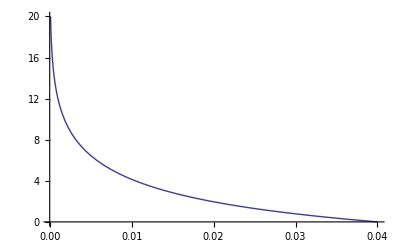

```mathematica
h=10;
t=0.01;
k=3;
γ=Sqrt [2*h/(k*t)];
Subscript[T, 0]=30;
Subscript[T, 1]=40;
Subscript[T, a]=10;
Subscript[θ, 0]=Subscript[T, 0]-Subscript[T, a];
Subscript[θ, 1]=Subscript[T, 1]-Subscript[T, a];
Subscript[r, 1]=0.0001;
Subscript[r, 2]=0.04;
solution2=NDSolve[{θ''[r]+1/r *θ'[r] - γ^2 *θ[r]== 0,θ[Subscript[r, 1]]==Subscript[θ, 0],θ[Subscript[r, 2]]==0},θ,{r,Subscript[r, 1],Subscript[r, 2]}];
PS2=Plot[Evaluate[θ[r]/.First[solution2]],{r,Subscript[r, 1],Subscript[r, 2]},PlotRange->All]
```

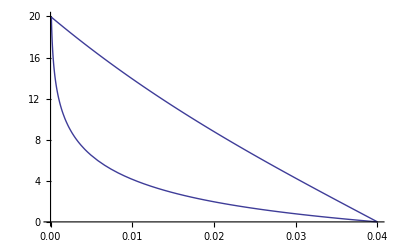

```mathematica
Show [PS1,PS2]
```

```mathematica
h = 10. ;
(*W/m^2C *)
k = 3. ;
(*W/mC *)
ALPHA = 2*10^-6
(*kg/m^3 x J/kg C*)
Tenv = 10. ;
(* °C *)
Acs = W*THICK;
(*cross sectional area m^2 *)
P = 2*(W+THICK);
(* Perimeter meters ^2 *)
HPKA = (h*P*k*Acs)^0.5;
TEMP = To-Tenv;
m=(h*P/(k*Acs))^0.5;
```

-Graphics-

1/500000

40.

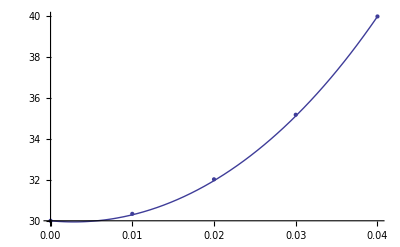

```mathematica
(* Fin Analytical Solutions - See p. 46 - Table in INTROHT pdf *)

Subscript[x, 1]=0.0;
Subscript[x, 2]=0.04;
L =Subscript[x, 2] - Subscript[x, 1];

(*meter*)
To = 30. ;
(* °C *)
Tend=40. ;
(* °C *)
W= 0.01;
(*meter*)
THICK=1. ;
(*meters*)
h = 10. ;
(*W/m^2C *)
k = 3. ;
(*W/mC *)
ALPHA = 2*10^-6
(*kg/m^3 x J/kg C*)
Tenv = 10. ;
(* °C *)
Acs = W*THICK;
(*cross sectional area m^2 *)
P = 2*(W+THICK);
(* Perimeter meters ^2 *)
HPKA = (h*P*k*Acs)^0.5;
TEMP = To-Tenv;
m=(h*P/(k*Acs))^0.5;


x = L;
T = Tenv+TEMP*(Cosh [m(L-x)]+(h/(m*k))*Sinh[m(L-x)])/(Cosh [m*L]+(h/(m*k))*Sinh[m*L]);
T=Tenv+TEMP*(Cosh [m(L-x)])/(Cosh [m*L]);
T= Tenv+TEMP*Exp[-m*x];
T= Tenv+TEMP*((((Tend-Tenv)/TEMP)*Sinh[m*x])+Sinh[m(L-x)])/Sinh[m*L]

m  = 26;
INFTIP = m*L;
Plot1 = Plot[Tenv+TEMP*(Cosh [m(L-x)]+(h/(m*k))*Sinh[m(L-x)])/(Cosh [m*L]+(h/(m*k))*Sinh[m*L]),{x,0,L}];
(* Adiabatic Tip *)
Plot2 = Plot[Tenv+TEMP*(Cosh [m(L-x)])/(Cosh [m*L]),{x,0,L}];
(* Insulated Tip *)
Plot3 = Plot[Tenv+TEMP*Exp[-m*x],{x,0,L}];
(* Infinite Tip  - good for mL > 2.3 *)
Plot4= Plot[ Tenv+TEMP*((((Tend-Tenv)/TEMP)*Sinh[m*x])+Sinh[m(L-x)])/Sinh[m*L],{x,0,L}];
(* Prescribed Tip Condition *)

PlotFINDIF = ListPlot [{{0,30},{0.01,30.34},{0.02,32.03},{0.03, 35.19},{0.04,40.}},PlotStyle->PointSize->Large];

Show [Plot4, PlotFINDIF,PlotRange ->All]
```

```mathematica
(* Homework asking them to calculate Fin Heat Transfer Rates *)
```